```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[T,β]
```

```mathematica
Clear[LEFT,leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["~/Downloads/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,3,0.01]}]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+01]]]
```

```mathematica
LEFT[0,10]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentrationk;;]=Table[SortBy[Join[RandomSample[Join[s[1,50,1,25]],concentration],RandomSample[Join[s[1,50,26,50]],total-concentration]],First],1000]
```

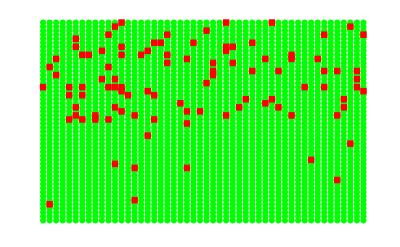

```mathematica
ListPlot[{Join[s[1,50,1,50]],dist[100,10][[30]]},PlotMarkers->Automatic,PlotStyle->{Green,Red,Black},Axes->False]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,1,10}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;10,1;;10]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=10},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,10].SLLEAD[ω,10].T[1,10]].g[ω,0.0001,1,0]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_]:= Module[{sizeoflead=10},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[total,concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[total,concentration][[number]][[loc1,2]],dist[total,concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[total,concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[total,concentration][[number]][[loc1,2]],dist[total,concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

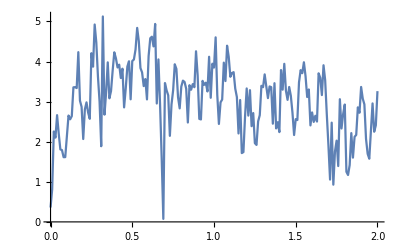

```mathematica
ListLinePlot[ParallelTable[{ω,CA[ω,0.0001,1,0,0,100,10,1]},{ω,0,2,0.01}]]
```

```mathematica
Monitor[Table[{c,Mean[ParallelTable[CA[0.0,0.0001,1,0,0.5,100,c,n],{n,1000}]]},{c,5,95,10}],c]
```

{{5,2.87881},{15,3.03617},{25,3.10102},{35,3.25077},{45,3.46208},{55,3.45168},{65,3.61538},{75,3.51638},{85,3.65155},{95,3.79006}}

```mathematica
Monitor[Table[Export["~/PhD_new/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/100_up_"<>ToString[x]<>"_.dat",Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,0.5,100,x,n],{n,1000}]]},{ω,Range[0,3,0.01]}]],{x,5,95,5}],x]
```

$Aborted

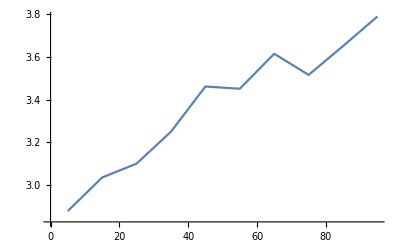

```mathematica
ListPlot[%230,Joined->True]
```

```mathematica
ParallelTable[CA[ω,0.0001,1,0,0,100,40,2],{ω,0,3,0.01}]//ListLinePlot
```

$Aborted

```mathematica
Table[Import["~/PhD_new/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/100_up_"<>ToString[x]<>"_.dat"],{x,5,50,5}]
```

{{{0.,2.82746},{0.01,2.71338},{0.02,2.81278},{0.03,2.54145},{0.04,2.64248},{0.05,2.80501},{0.06,3.38442},287,{2.94,1.40927},{2.95,1.56502},{2.96,1.65518},{2.97,1.40929},{2.98,1.36556},{2.99,1.35657},{3.,1.0991}},8,{1}}
 |  |  |  |

```mathematica
Abs[%235[[1]][[;;,2]]-ParallelTable[CA[ω,0.0001,1,0,0.5,100,40,2],{ω,0,3,0.01}]]
```

```mathematica
Misfit= Table[Total[Abs[%235[[x]][[;;,2]]-ParallelTable[CA[ω,0.0001,1,0,0.5,100,40,2],{ω,0,3,0.01}]]],{x,6}]
```

{157.713,145.249,152.976,150.816,160.053,157.096}

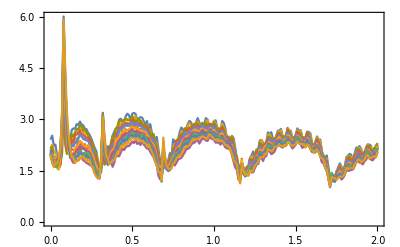

```mathematica
ListLinePlot[Join[Table[Import["~/PhD_new/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/size_5_asy_"<>ToString[x]<>"_.dat"],{x,5,45,5}],Table[Import["~/PhD_new/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/size_10_asy_"<>ToString[x]<>"_.dat"],{x,5,40,5}]],PlotRange->All,Frame->True]
```